Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Left Discontinuous

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Right Discontinuous

left limit = right limit

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Discontinuous

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

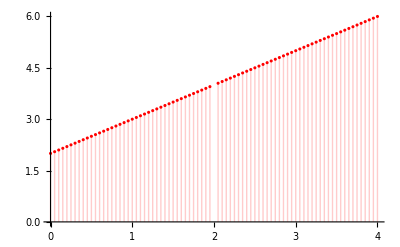

```mathematica
f[x_]:=(x^2 -4)/(x - 2);
point=2;
(* Defining left limit and right limit of the function *)
leftLim[k_, x_, p_]:=Limit[k[x], x->p,Direction->-1];
rightLim[k_, x_, p_]:=Limit[k[x], x->p,Direction->1];


If[leftLim[f,x,point] === f[point], "Left Continuous", "Left Discontinuous"]
If[rightLim[f,x,point] === f[point], "Right Continuous", "Right Discontinuous"]
If[leftLim[f,x,point]===rightLim[f,x,point], "left limit = right limit", "left limit ≠ right limit"] (* left limit = right limit but they ≠ f(2), so discontinuous *)
If[leftLim[f,x,point]===rightLim[f,x,point] === f[point], "Continuous", "Discontinuous"]

DiscretePlot[f[x],{x,0,4,0.05},AxesOrigin->{0,0},PlotRange->Full,PlotStyle->{Red,Thick}]
```

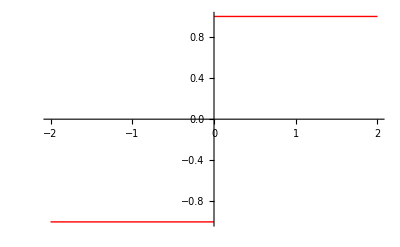

Left Discontinuous

Right Discontinuous

left limit ≠ right limit

Discontinuous

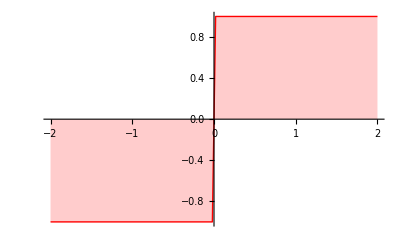

```mathematica
f[x_]:=Piecewise[{{-1,x<0},{1,x>0}, {0, x==0}}];  
Plot[f[x],{x,-2,2},PlotStyle->{Red,Thick}]
point=0;
(* Defining left limit and right limit of the function *)
leftLim[k_, x_, p_]:=Limit[k[x], x->p,Direction->-1];
rightLim[k_, x_, p_]:=Limit[k[x], x->p,Direction->1];

If[leftLim[f,x,point] === f[point], "Left Continuous", "Left Discontinuous"]
If[rightLim[f,x,point] === f[point], "Right Continuous", "Right Discontinuous"]
If[leftLim[f,x,point]===rightLim[f,x,point], "left limit = right limit", "left limit ≠ right limit"] 
If[leftLim[f,x,point]===rightLim[f,x,point] === f[point], "Continuous", "Discontinuous"]
DiscretePlot[f[x],{x,0-2,2,0.02},AxesOrigin->{0,0},PlotRange->Full,PlotStyle->{Red,Thick}]
```

Left Continuous

Right Continuous

left limit = right limit

Continuous

Continuous

Continuous

Not Differentiable

Not Differentiable

Differentiable

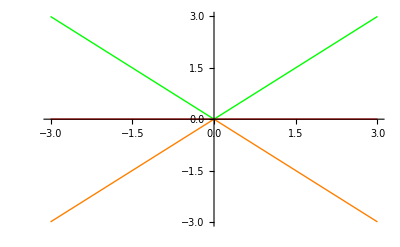

```mathematica
f[x_]:=Piecewise[{{-x,x<0},{x,x>0}}];  (* f(x)=|x| , not differenetiable at x=0 *) 
g[x_]:=Piecewise[{{x,x<0},{-x,x>0}}]; (* g(x)=-|x| , not differentiable at x=0 *)
h[x_]:=f[x]+g[x];           (* h(x)=f(x)+g(x) , differenetiable at x=0 *)

point=0;         (* Check differentiability by changing the point *)

(* D[f[x],x]/.x->point
D[g[x],x]/.x->point 
D[h[x],x]/.x->point *)

(*Simplify[h[x]]*)
(*leftDeriv=Limit[(h[x]-h[point])/(x-point), x->0,Direction->-1];
rightDeriv=Limit[(h[x]-h[point])/(x-point), x->0,Direction->1];
If[leftDeriv===rightDeriv, "Differentiable", "Not Differentiable"]*)

(* Defining left limit and right limit of the function *)
leftLim[k_, x_, p_]:=Limit[k[x], x->p,Direction->-1];
rightLim[k_, x_, p_]:=Limit[k[x], x->p,Direction->1];

(* Defining left derivative and right derivative *)
leftDeriv[k_,x_,p_]:=Limit[(k[x]-k[p])/(x-p), x->p,Direction->-1];
rightDeriv[k_,x_,p_]:=Limit[(k[x]-k[p])/(x-p), x->p,Direction->1];

If[leftLim[f,x,point] === f[point], "Left Continuous", "Left Discontinuous"]
If[rightLim[f,x,point] === f[point], "Right Continuous", "Right Discontinuous"]
If[leftLim[f,x,point]===rightLim[f,x,point], "left limit = right limit", "left limit ≠ right limit"]

If[leftLim[f,x,point]===rightLim[f,x,point] === f[point], "Continuous", "Discontinuous"]
If[leftLim[g,x,point]===rightLim[g,x,point] === g[point], "Continuous", "Discontinuous"]
If[leftLim[h,x,point]===rightLim[h,x,point] === h[point], "Continuous", "Discontinuous"]

If[leftDeriv[f,x,point]===rightDeriv[f,x,point], "Differentiable", "Not Differentiable"]  (* continuous but has notch at x=0 *)
If[leftDeriv[g,x,point]===rightDeriv[g,x,point], "Differentiable", "Not Differentiable"]  (* continuous but has notch at x=0 *)
If[leftDeriv[h,x,point]===rightDeriv[h,x,point], "Differentiable", "Not Differentiable"]  (* continuous and has no notch at x=0 *)

(* (f(x) + g(x)) is a horizontal line through x-axis and differentiable at all points including x=0. Its derivative at each point is 0 *)
Plot[{f[x],g[x],(f[x]+g[x])}, {x,-3,3},PlotStyle->{Directive[Green,Thick],Directive[Orange,Thick],Directive[Red,Thick]}]
```

SetDelayed::write: Tag Check in Check[r_,x_,p_] is Protected.

Indeterminate

Indeterminate

1

-1

0

0

0

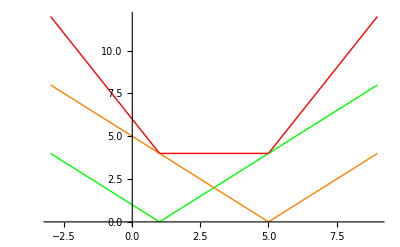

```mathematica
f[x_]:=Piecewise[{{-(x-1),x<1},{(x-1),x>1}}];  (* f(x)=|x-1|, decreasing below x=1 nad increasing above x>1. Not differentiable at x=1 *)
g[x_]:=Piecewise[{{-(x-5),x<5},{(x-5),x>5}}];  (* g(x)=|x-5|, decreasing below x=5 nad increasing above x>5. Not differentiable at x=5 *)
h[x_]:=f[x]+g[x];           (* h(x)=f(x)+g(x) *)

leftDeriv[k_,x_,p_]:=Limit[(k[x]-k[p])/(x-p), x->p,Direction->-1];
rightDeriv[k_,x_,p_]:=Limit[(k[x]-k[p])/(x-p), x->p,Direction->1];

Check[r_,x_,p_]:=If[leftDeriv[r,x,p]===rightDeriv[r,x,p], "Differentiable", "Not Differentiable"];
(*Check[k_,x_,p_]:=Module[{ld,rd},
ld=leftDeriv[k,x,p];
rd=rightDeriv[k,x,p];
If[NumericQ[ld]&&NumericQ[rd]&&ld==rd,"Differentiable","Not Differentiable"]];*)


(*If[leftDeriv[f,x,1]===rightDeriv[f,x,1], "Differentiable", "Not Differentiable"]
If[leftDeriv[g,x,5]===rightDeriv[g,x,5], "Differentiable", "Not Differentiable"]
If[leftDeriv[h,x,1]===rightDeriv[h,x,1], "Differentiable", "Not Differentiable"]
If[leftDeriv[h,x,5]===rightDeriv[h,x,5], "Differentiable",  "Not Differentiable"]
If[leftDeriv[h,x,3]===rightDeriv[h,x,3], "Differentiable", "Not Differentiable"]*)

(*Check[h,x,3]*)

D[f[x],x]/.x->1
D[g[x],x]/.x->5

D[f[x],x]/.x->3
D[g[x],x]/.x->3
D[h[x],x]/.x->3
D[h[x],x]/.x->2
D[h[x],x]/.x->4

(* f(x) + g(x) is a horizontal line (y=4) parallel to x-axis at 1<x<5, decreasing below x=1, and increasing above x>5 . Its derivative at each points in between 1<x<5 is 0. *)
Plot[{f[x],g[x],(f[x]+g[x])}, {x,-3,9},PlotStyle->{Directive[Green,Thick],Directive[Orange,Thick],Directive[Red,Thick]}]
```

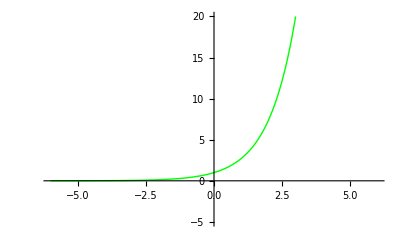

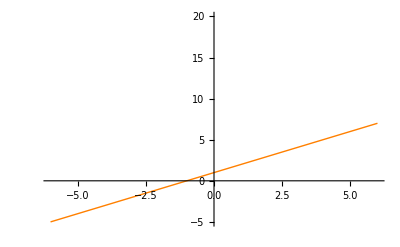

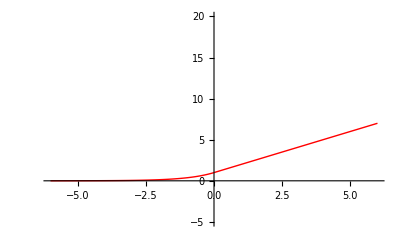

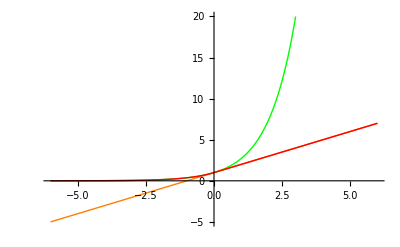

Left Continuous

Right Continuous

left limit = right limit

Continuous

Differentiable

```mathematica
f[x_]:=Piecewise[{{Exp[x],x<0},{(x+1),x≥0}}];      (* continuous and has no notch at x=0 *)

Plot[Exp[x], {x,-6,6},PlotStyle->Directive[Green,Thick],PlotRange->{{-6,6},{-5,20}}]    
Plot[ x+1, {x,-6,6},PlotStyle->Directive[Orange,Thick],PlotRange->{{-6,6},{-5,20}}]
Plot[f[x], {x,-6,6},PlotStyle->Directive[Red,Thick],PlotRange->{{-6,6},{-5,20}}]
Plot[{Exp[x], x+1, f[x]}, {x,-6,6},PlotStyle->{Directive[Green,Thick],Directive[Orange,Thick],Directive[Red,Thick]},PlotRange->{{-6,6},{-5,20}}]

point=0;

leftLim[k_, x_, p_]:=Limit[k[x], x->p,Direction->-1];
rightLim[k_, x_, p_]:=Limit[k[x], x->p,Direction->1];

leftDeriv[k_,x_,p_]:=Limit[(k[x]-k[p])/(x-p), x->p,Direction->-1];
rightDeriv[k_,x_,p_]:=Limit[(k[x]-k[p])/(x-p), x->p,Direction->1];

If[leftLim[f,x,point] === f[point], "Left Continuous", "Left Discontinuous"]
If[rightLim[f,x,point] === f[point], "Right Continuous", "Right Discontinuous"]
If[leftLim[f,x,point]===rightLim[f,x,point], "left limit = right limit", "left limit ≠ right limit"]
If[leftLim[f,x,point]===rightLim[f,x,point] === f[point], "Continuous", "Discontinuous"]
If[leftDeriv[f,x,point]===rightDeriv[f,x,point], "Differentiable", "Not Differentiable"]
```

-Graphics-

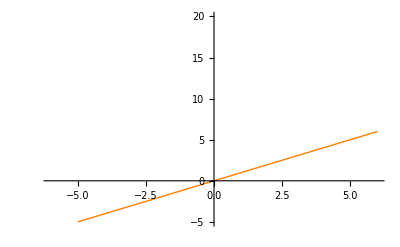

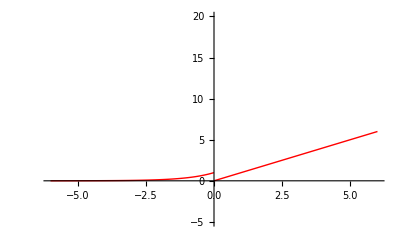

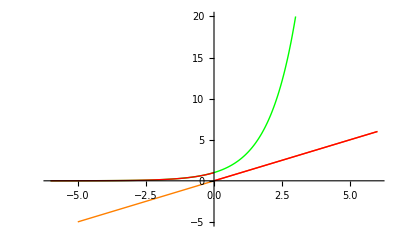

Left Continuous

Right Discontinuous

left limit ≠ right limit

Discontinuous

Not Differentiable

```mathematica
f[x_]:=Piecewise[{{Exp[x],x<0},{(x),x≥0}}];            (* discontinuous at x=0 *)

Plot[Exp[x], {x,-6,6},PlotStyle->Directive[Green,Thick],PlotRange->{{-6,6},{-5,20}}]   
Plot[ x, {x,-6,6},PlotStyle->Directive[Orange,Thick],PlotRange->{{-6,6},{-5,20}}]
Plot[f[x], {x,-6,6},PlotStyle->Directive[Red,Thick],PlotRange->{{-6,6},{-5,20}}]                                                                     
Plot[{Exp[x], x, f[x]}, {x,-6,6},PlotStyle->{Directive[Green,Thick],Directive[Orange,Thick],Directive[Red,Thick]},PlotRange->{{-6,6},{-5,20}}]

point=0;

leftLim[k_, x_, p_]:=Limit[k[x], x->p,Direction->-1];
rightLim[k_, x_, p_]:=Limit[k[x], x->p,Direction->1];

leftDeriv[k_,x_,p_]:=Limit[(k[x]-k[p])/(x-p), x->p,Direction->-1];
rightDeriv[k_,x_,p_]:=Limit[(k[x]-k[p])/(x-p), x->p,Direction->1];

If[leftLim[f,x,point] === f[point], "Left Continuous", "Left Discontinuous"]
If[rightLim[f,x,point] === f[point], "Right Continuous", "Right Discontinuous"]
If[leftLim[f,x,point]===rightLim[f,x,point], "left limit = right limit", "left limit ≠ right limit"]
If[leftLim[f,x,point]===rightLim[f,x,point] === f[point], "Continuous", "Discontinuous"]
If[leftDeriv[f,x,point]===rightDeriv[f,x,point], "Differentiable", "Not Differentiable"]
```

-Graphics-

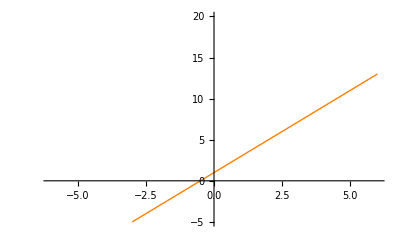

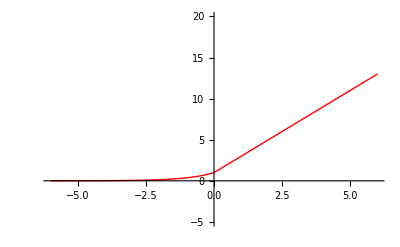

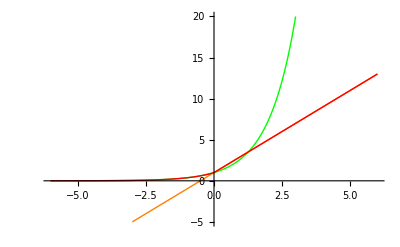

Left Continuous

Right Continuous

left limit = right limit

Continuous

Not Differentiable

```mathematica
f[x_]:=Piecewise[{{Exp[x],x<0},{(2x+1),x≥0}}];         (* continuous but has notch at x=0 *)

Plot[Exp[x], {x,-6,6},PlotStyle->Directive[Green,Thick],PlotRange->{{-6,6},{-5,20}}]
Plot[2 x+1, {x,-6,6},PlotStyle->Directive[Orange,Thick],PlotRange->{{-6,6},{-5,20}}]
Plot[f[x], {x,-6,6},PlotStyle->Directive[Red,Thick],PlotRange->{{-6,6},{-5,20}}]
Plot[{Exp[x], 2x+1, f[x]}, {x,-6,6},PlotStyle->{Directive[Green,Thick],Directive[Orange,Thick],Directive[Red,Thick]},PlotRange->{{-6,6},{-5,20}}]

point=0;

leftLim[k_, x_, p_]:=Limit[k[x], x->p,Direction->-1];
rightLim[k_, x_, p_]:=Limit[k[x], x->p,Direction->1];

leftDeriv[k_,x_,p_]:=Limit[(k[x]-k[p])/(x-p), x->p,Direction->-1];
rightDeriv[k_,x_,p_]:=Limit[(k[x]-k[p])/(x-p), x->p,Direction->1];

If[leftLim[f,x,point] === f[point], "Left Continuous", "Left Discontinuous"]
If[rightLim[f,x,point] === f[point], "Right Continuous", "Right Discontinuous"]
If[leftLim[f,x,point]===rightLim[f,x,point], "left limit = right limit", "left limit ≠ right limit"]
If[leftLim[f,x,point]===rightLim[f,x,point]=== f[point], "Continuous", "Discontinuous"]
If[leftDeriv[f,x,point]===rightDeriv[f,x,point], "Differentiable", "Not Differentiable"]
```

```mathematica
f[x_,y_]:=Piecewise[{{x/√(x^2+y^2),{x, y}≠{0,0}},{0, {x,y}==={0, 0}}}];  
Plot3D[f[x,y],{x,-2,2},{y,-2,2}, Mesh->None]
(* DensityPlot[f[x,y],{x,-2,2},{y,-2,2}] *)
(* ContourPlot[f[x,y],{x,-2,2},{y,-2,2}] *)
point={0,0};
(* Defining left limit and right limit of the function *)
Lim1[k_, x_, y_, p_]:=Limit[k[x,y], {x,y}->p,Direction->{1, 1}]; (* Approaching from first first quadrant *)
Lim2[k_, x_, y_, p_]:=Limit[k[x,y], {x,y}->p,Direction->{-1, 1}]; (* Approaching from second first quadrant *)
Lim3[k_, x_, y_, p_]:=Limit[k[x,y], {x,y}->p,Direction->{-1, -1}]; (* Approaching from third first quadrant *)
Lim4[k_, x_, y_, p_]:=Limit[k[x,y], {x,y}->p,Direction->{1, -1}]; (* Approaching from fourth first quadrant *)


If[Lim1[f,x,y,point] === f[point], "Right-Above Continuous", "Right-Above Discontinuous"]
If[Lim2[f,x,y,point] === f[point], "Left-Above Continuous", "Left-Above Discontinuous"]
If[Lim3[f,x,y,point] === f[point], "Left-Below Continuous", "Left-Below Discontinuous"]
If[Lim4[f,x,y,point] === f[point], "Right-Below Continuous", "Right-Below Discontinuous"]

If[Lim1[f,x,y,point]=== Lim2[f,x,y,point], "Right-Above limit = Left-Above limit", "Right-Above limit ≠ Left-Above limit"] 
If[Lim1[f,x,y,point]=== Lim3[f,x,y,point], "Right-Above limit = Left-Below limit", "Right-Above limit ≠ Left-Below limit"] 
If[Lim1[f,x,y,point]=== Lim4[f,x,y,point], "Right-Above limit = Right-Below limit", "Right-Above limit ≠ Right-Below limit"] 
If[Lim2[f,x,y,point]=== Lim3[f,x,y,point], "Left-Above limit = Left-Below limit", "Left-Above limit ≠ Left-Below limit"] 
If[Lim2[f,x,y,point]=== Lim4[f,x,y,point], "Left-Above limit = Right-Below limit", "Left-Above limit ≠ Right-Below limit"] 
If[Lim3[f,x,y,point]=== Lim4[f,x,y,point], "Left-Below limit = Right-Below limit", "Left-Below limit ≠ Right-Below limit"] 
If[Lim1[f,x,y,point]=== Lim2[f,x,y,point] === Lim3[f,x,y,point]=== Lim4[f,x,y,point]=== f[point], "Continuous", "Discontinuous"]
```

-Graphics3D-

Right-Above Discontinuous

Left-Above Discontinuous

Left-Below Discontinuous

Right-Below Discontinuous

Right-Above limit = Left-Above limit

Right-Above limit = Left-Below limit

Right-Above limit = Right-Below limit

Left-Above limit = Left-Below limit

Left-Above limit = Right-Below limit

Left-Below limit = Right-Below limit

Discontinuous